## Bivariate Von Mises distributions

```mathematica
VonMises2D[x1_,x2_ ,k1_,k2_,m1_,m2_,lcc_, lcs_,lsc_,lss_]:=Exp[k1*Cos[(x1-m1)] + k2*Cos[(x2-m2)] + lcc*Cos[(x1-m1)]*Cos[(x2-m2)] + lcs*Cos[(x1-m1)]*Sin[(x2-m2)] +lsc*Sin[(x1-m1)]*Cos[(x2-m2)] +  lss*Sin[(x1-m1)]*Sin[(x2-m2)]]
```

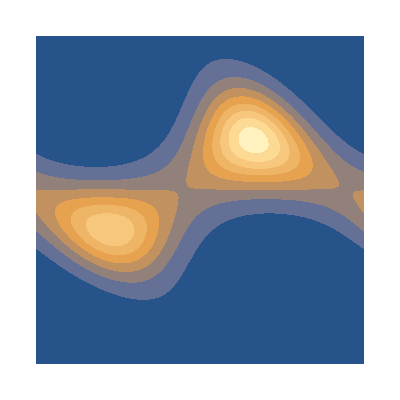

```mathematica
ContourPlot[VonMises2D[x1,x2,1,2,0,0.2,-1,0.7,0,2],{x1,-Pi,Pi},{x2,-Pi,Pi}, AxesLabel->None, ColorFunction->Automatic,Ticks->None,Frame->False,ContourLines->False]
```

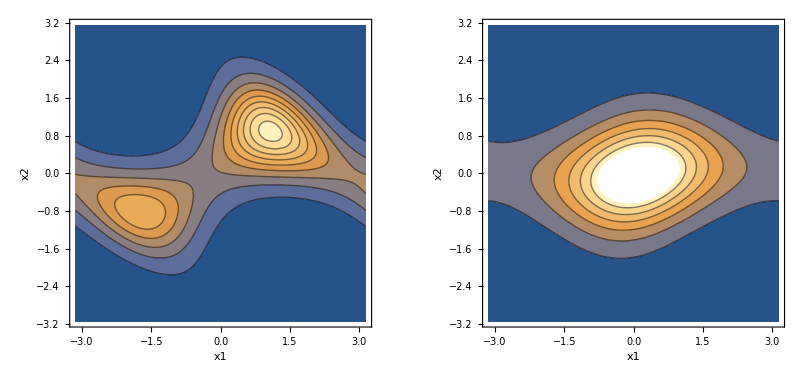

```mathematica
k1 = 1; k2 = 2; m1 = 0; m2 = 0;lcc = -1; lcs = 0.7; lsc = 0.2; lss = 2;GraphicsRow[{ContourPlot[VonMises2D[x1,x2,k1,k2,m1,m2,lcc,lcs,lsc,lss],{x1,-Pi,Pi},{x2,-Pi,Pi}, AxesLabel->Automatic] ,
lcc = -.1; lcs = -.1; lsc = .1; lss = .3;ContourPlot[VonMises2D[x1,x2,k1,k2,m1,m2,lcc,lcs,lsc,lss],{x1,-Pi,Pi},{x2,-Pi,Pi}, AxesLabel->Automatic]}]
```

```mathematica
k1 = 1; k2 = 1; m1 = 0; m2 = 0;lcc =  0; lcs = 0.4; lsc = 0; lss = 2;Plot3D[VonMises2D[x1,x2,k1,k2,m1,m2,lcc,lcs,lsc,lss],{x1,-Pi,Pi},{x2,-Pi,Pi}, PlotRange->All, Mesh->Automatic, MeshStyle->White, AxesLabel->None, Boxed->False, Axes->False,PlotStyle->RGBColor[0.85,0.3,0], Background->None]
```

-Graphics3D-

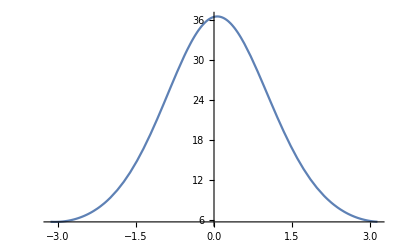

```mathematica
Plot[NIntegrate[VonMises2D[x1,x2,k1,k2,m1,m2,lcc,lcs,lsc,lss],{x2,-Pi,Pi}],{x1,-Pi,Pi}]
```

```mathematica
F[x1_,x2_ ,A_,A2_,B_,B2_,lcc_, lcs_,lsc_,lss_,m1_,m2_]:=Exp[A*Cos[x1] + A2*Cos[2*x1] + B*Sin[x1] + B2*Sin[2*x1] + lcc*Cos[(x1-m1)]*Cos[(x2-m2)] + lcs*Cos[(x1-m1)]*Sin[(x2-m2)] +lsc*Sin[(x1-m1)]*Cos[(x2-m2)] +  lss*Sin[(x1-m1)]*Sin[(x2-m2)]]
```

```mathematica
Manipulate[ContourPlot[F[x1,x2,A,A2,B,B2,lcc,lcs,lsc,lss,0,0],{x1,-Pi,Pi},{x2,-Pi,Pi}, PlotRange->All, Mesh->Automatic,AxesLabel->Automatic],{A,-1,1},{A2,-1,1}, {B,-1,1},{B2,-1,1}, {lcc,-1,1},{lcs,-1,1},{lsc,-1,1},{lss,-1,1}]
```

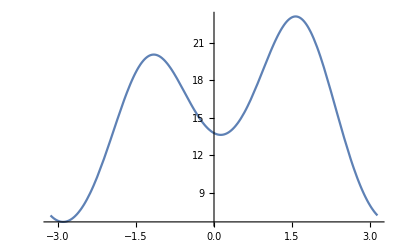

```mathematica
A = 1; A2 = -0.5; B = 0; B2 = 0; lcc = 1; lcs = 0.5; lsc = 0.5; lss = -2;
Plot[NIntegrate[F[x1,x2,A,A2,B,B2,lcc,lcs,lsc,lss,0,0],{x1,-Pi,Pi}],{x2,-Pi,Pi},PlotRange->All]
```

```mathematica
Integrate[F[x1,x2,A,A2,B,B2,lcc,lcs,lsc,lss],{x1,-Pi,Pi}]
```

∫_-π^π ⅇ^(Cos[x1]-0.5 Cos[2 x1]+Cos[x1] Cos[x2]+0.5 Cos[x2] Sin[x1]+0.5 Cos[x1] Sin[x2]-2 Sin[x1] Sin[x2])ⅆx1

```mathematica
GenVonMises[x_,k1_,k2_,m1_,m2_]:=Exp[k1*Cos[x - m1]+ k2*Cos[2*(x - m2)]]
```

```mathematica
Manipulate[Plot[GenVonMises[x,k1,k2,0, dm],{x,-Pi,Pi}],{k1,0,2},{k2,0,2},{dm,-Pi,Pi}]
```

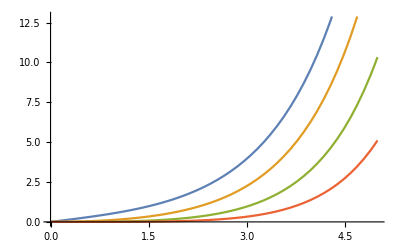

```mathematica
Plot[{BesselI[1,x],BesselI[2,x],BesselI[3,x],BesselI[4,x]},{x,0,5}]
```

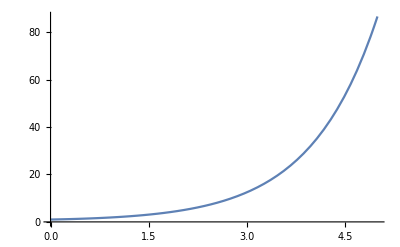

```mathematica
Plot[Sum[BesselI[n,x],{n,0,5}],{x,0,5}]
```

```mathematica
Manipulate[Plot[Sum[BesselI[n,x],{n,0,m}],{x,0,5}],{m,1,5,1}]
```